```mathematica
(* Simplex Algorithm Written by Kyle Salitrik *)
$Line=0;
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
RemoveGlobal[];
```

```mathematica
(* Pivot Function *)
pivot[m_,iStar_, jStar_] :=(
(* Create copy of matrix  and get dimensions *)
mm=m;
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
(* Begin Pivoting *)
mm[[1,jStar] ]=m[[iStar,cols]]; 
mm[[iStar,cols]]=m[[1,jStar]];
For[row=2, row≤rows, row++,
For[col=1,col<cols,col++,
{
(* P *)
If[row==iStar && col==jStar,
mm[[row,col]]=1/m[[iStar,jStar]]],
(* Q *)
If[row==iStar && col ≠ jStar,
mm[[row,col]]=-m[[row,col]]/m[[iStar, jStar]]],
(* R *)
If[row≠iStar && col== jStar,
mm[[row,col]]=m[[row,col]]/m[[iStar, jStar]]],
(* S *)
If[row≠iStar && col ≠ jStar,
mm[[row,col]]=m[[row,col]]-m[[iStar,col]]m[[row,jStar]]/m[[iStar,jStar]]]
}
]
];
Return[mm];
)
```

```mathematica
(* Max Test Function: Returns the index of the max value. *)
maxTest[m_,jStar_,i0_]:=(
(* Get jth column *)
rows=Dimensions[m][[1]];

(* Create temporary array to get max position from *)
compArray={0};

(* Get negative column values and divide by corresponding b_i value*)
For[row=2, row<rows, row++,
If[m[[row,jStar]] < 0 || row==i0,
AppendTo[compArray,m[[row,jStar]]/m[[row,cols-1]]],
AppendTo[compArray,0]
]
];
Return [Position[compArray,Min[compArray]]]
)
```

```mathematica
(* Blands rule: Returns the correct variable to use based on blands rule if ties occur during the Simplex Algorithm *)
blandsRule[potentialSolutions_, blandVector_]:=(
Return[Min[Position[blandVector,Alternatives@@potentialSolutions]]]
)
```

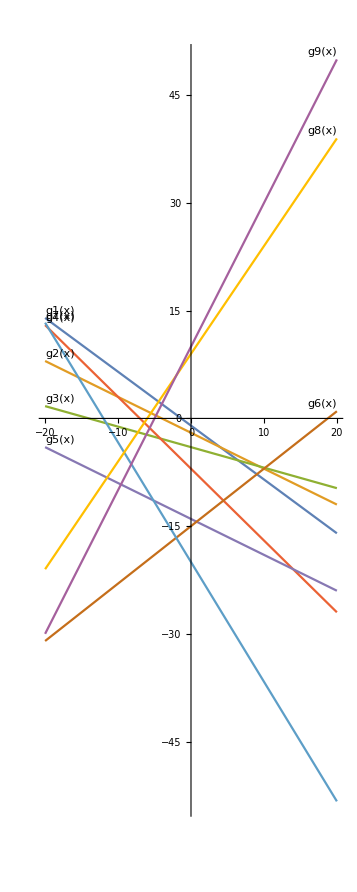

```mathematica
(* Define Boundary Functions *)
g1[x_,y_]:=-3x-4y;
g2[x_,y_]:=x+2y;
g3[x_,y_]:=-2x-7y;
g4[x_,y_]:=2x+2y;
g5[x_,y_]:=x+2y;
g6[x_,y_]:=-4x+5y;
g7[x_,y_]:=5x+3y;
g8[x_,y_]:=-3x+2y;
g9[x_,y_]:=-2x+y;

b1=4;b2=-4;b3=28;b4=-14;b5=-28;b6=-75;b7=-60;b8=18;b9=10;

g1[x_]:=y/.Solve[g1[x,y]==b1,{y}][[1,1]]
g2[x_]:=y/.Solve[g2[x,y]==b2,{y}][[1,1]]
g3[x_]:=y/.Solve[g3[x,y]==b3,{y}][[1,1]]
g4[x_]:=y/.Solve[g4[x,y]==b4,{y}][[1,1]]
g5[x_]:=y/.Solve[g5[x,y]==b5,{y}][[1,1]]
g6[x_]:=y/.Solve[g6[x,y]==b6,{y}][[1,1]]
g7[x_]:=y/.Solve[g7[x,y]==b7,{y}][[1,1]]
g8[x_]:=y/.Solve[g8[x,y]==b8,{y}][[1,1]]
g9[x_]:=y/.Solve[g9[x,y]==b9,{y}][[1,1]]

Plot[{g1[x],g2[x],g3[x],g4[x],g5[x],g6[x],g7[x],g8[x],g9[x]},{x,-20,20},{AspectRatio->Automatic},PlotLabels->Placed[Automatic,Above]]
```

```mathematica
(* Defining all constraints with ≤ *)
(*  3x + 4y ≤ -04 *)
(*   x + 2y ≤ -04 *)
(*  2x + 7y ≤ -28 *)
(*  2x + 2y ≤ -14 *)
(* - x - 2y ≤  28 *)
(*  4x - 5y ≤  75 *)
(* -5x - 3y ≤  60 *)
(* -3x + 2y ≤  18 *)
(* -2x +  y ≤  10 *)

(* Adding in and solving for slack variables *)
(* s1 = -04 - 3x - 4y *)
(* s2 = -04 - 1x - 2y *)
(* s3 = -28 - 2x - 7y *)
(* s4 = -14 - 2x - 2y *)
(* s5 =  28 + 1x + 2y *)
(* s6 =  75 - 4x + 5y *)
(* s7 =  60 + 5x + 3y *)
(* s8 =  18 + 3x - 2y *)
(* s9 =  10 + 2x - 1y *)

(* Substituting x1= v1-v2,x2=v2-v4 into tableau*)
(* Objective function becomes: 10v1 - 10v2 + 6v3 - 6v4 - 12 *)

(* Create vector of variables for Bland's Rule *)
blandVector = {v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9}

(* Defining t0 *)
m0={v1,v2,v3,v4,1,""};
m1 ={-3,3,-4,4,-04,s1};
m2 ={-1,1,-2,2,-04,s2};
m3 ={-2,2,-7,7,-28,s3};
m4 ={-2,2,-2,2,-14,s4};
m5 ={ 1,-1,2,-2,28,s5};
m6 ={-4,4,5,-5,75,s6};
m7 ={5,-5,3,-3,60,s7};
m8 ={3,-3,-2,2,18,s8};
m9 ={2,-2,-1,1,10,s9};
mobj={10,-10,6,-6,-12,z->min};
t0={m0,m1,m2,m3,m4,m5,m6,m7,m8,m9,mobj};
Print["t0 = ",MatrixForm[t0]]
```

{v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9}

t0 = (v1 | v2 | v3 | v4 | 1 | 
-3 | 3 | -4 | 4 | -4 | s1
-1 | 1 | -2 | 2 | -4 | s2
-2 | 2 | -7 | 7 | -28 | s3
-2 | 2 | -2 | 2 | -14 | s4
1 | -1 | 2 | -2 | 28 | s5
-4 | 4 | 5 | -5 | 75 | s6
5 | -5 | 3 | -3 | 60 | s7
3 | -3 | -2 | 2 | 18 | s8
2 | -2 | -1 | 1 | 10 | s9
10 | -10 | 6 | -6 | -12 | z→min)

```mathematica
(* i0 = 2, since it's first row, no need to use max test *)
(* jStar is possibly 2 or 4, but bland's rule breaks the tie for 2 *)
(* iStar = 2 *)
(* jStar = 2 *)

t1 = pivot[t0,2,2];
Print["t1 = ",MatrixForm[t1]]
```

t1 = (v1 | s1 | v3 | v4 | 1 | 
1 | 1/3 | 4/3 | -4/3 | 4/3 | v2
0 | 1/3 | -2/3 | 2/3 | -8/3 | s2
0 | 2/3 | -13/3 | 13/3 | -76/3 | s3
0 | 2/3 | 2/3 | -2/3 | -34/3 | s4
0 | -1/3 | 2/3 | -2/3 | 80/3 | s5
0 | 4/3 | 31/3 | -31/3 | 241/3 | s6
0 | -5/3 | -11/3 | 11/3 | 160/3 | s7
0 | -1 | -6 | 6 | 14 | s8
0 | -2/3 | -11/3 | 11/3 | 22/3 | s9
0 | -10/3 | -22/3 | 22/3 | -76/3 | z→min)

```mathematica
(* i0 = 3 *)
(* jStar can be 2 or 4. Bland's rule says v4 before s2. *)
(* jStar = 4 *)
(* iStar = 3 by max test*)
iStarCandidatesT2={(-4/4),(2/-8)}
Max[iStarCandidatesT2]
t2=pivot[t1,3,4];
Print["t2 = ",MatrixForm[t2]]
```

{-1,-1/4}

-1/4

t2 = (v1 | s1 | v3 | s2 | 1 | 
1 | 1 | 0 | -2 | -4 | v2
0 | -1/2 | 1 | 3/2 | 4 | v4
0 | -3/2 | 0 | 13/2 | -8 | s3
0 | 1 | 0 | -1 | -14 | s4
0 | 0 | 0 | -1 | 24 | s5
0 | 13/2 | 0 | -31/2 | 39 | s6
0 | -7/2 | 0 | 11/2 | 68 | s7
0 | -4 | 0 | 9 | 38 | s8
0 | -5/2 | 0 | 11/2 | 22 | s9
0 | -7 | 0 | 11 | 4 | z→min)

```mathematica
(* i0 = 2 *)
(* jStar can be 1 or 2. Bland's Rule says 1 *)
(* jStar = 1 *)
(* iStar = 2 because there is no other possible option *)
t3=pivot[t2,2,1];
Print["t3 = ",MatrixForm[t3]]
```

t3 = (v2 | s1 | v3 | s2 | 1 | 
1 | -1 | 0 | 2 | 4 | v1
0 | -1/2 | 1 | 3/2 | 4 | v4
0 | -3/2 | 0 | 13/2 | -8 | s3
0 | 1 | 0 | -1 | -14 | s4
0 | 0 | 0 | -1 | 24 | s5
0 | 13/2 | 0 | -31/2 | 39 | s6
0 | -7/2 | 0 | 11/2 | 68 | s7
0 | -4 | 0 | 9 | 38 | s8
0 | -5/2 | 0 | 11/2 | 22 | s9
0 | -7 | 0 | 11 | 4 | z→min)

```mathematica
(* i0 = 4 *)
(* jStar can only be 4 *) 
(* jStar = 4 *)
(* iStar = 4 by max test*)
t4=pivot[t3,4,4];
Print["t4 = ",MatrixForm[t4]]
```

t4 = (v2 | s1 | v3 | s3 | 1 | 
1 | -7/13 | 0 | 4/13 | 84/13 | v1
0 | -2/13 | 1 | 3/13 | 76/13 | v4
0 | 3/13 | 0 | 2/13 | 16/13 | s2
0 | 10/13 | 0 | -2/13 | -198/13 | s4
0 | -3/13 | 0 | -2/13 | 296/13 | s5
0 | 38/13 | 0 | -31/13 | 259/13 | s6
0 | -29/13 | 0 | 11/13 | 972/13 | s7
0 | -25/13 | 0 | 18/13 | 638/13 | s8
0 | -16/13 | 0 | 11/13 | 374/13 | s9
0 | -58/13 | 0 | 22/13 | 228/13 | z→min)

```mathematica
(* i0 = 5 *)
(* jStar can only be 2 *) 
(* jStar = 2 *)
(* iStar = 3 by max test*)
iStarCandidatesT5={(-7/84),(-2/76),(10/-198)}
Max[iStarCandidatesT5]
t5=pivot[t4,3,2];
Print["t5 = ",MatrixForm[t5]]
```

{-1/12,-1/38,-5/99}

-1/38

t5 = (v2 | v4 | v3 | s3 | 1 | 
1 | 7/2 | -7/2 | -1/2 | -14 | v1
0 | -13/2 | 13/2 | 3/2 | 38 | s1
0 | -3/2 | 3/2 | 1/2 | 10 | s2
0 | -5 | 5 | 1 | 14 | s4
0 | 3/2 | -3/2 | -1/2 | 14 | s5
0 | -19 | 19 | 2 | 131 | s6
0 | 29/2 | -29/2 | -5/2 | -10 | s7
0 | 25/2 | -25/2 | -3/2 | -24 | s8
0 | 8 | -8 | -1 | -18 | s9
0 | 29 | -29 | -5 | -152 | z→min)

```mathematica
(* i0 = 2 *)
(* jStar is 1 by bland's rule *) 
(* jStar = 1 *)
(* iStar = 2 by max test*)
t6=pivot[t5,2,1];
Print["t6 = ",MatrixForm[t6]]
```

t6 = (v1 | v4 | v3 | s3 | 1 | 
1 | -7/2 | 7/2 | 1/2 | 14 | v2
0 | -13/2 | 13/2 | 3/2 | 38 | s1
0 | -3/2 | 3/2 | 1/2 | 10 | s2
0 | -5 | 5 | 1 | 14 | s4
0 | 3/2 | -3/2 | -1/2 | 14 | s5
0 | -19 | 19 | 2 | 131 | s6
0 | 29/2 | -29/2 | -5/2 | -10 | s7
0 | 25/2 | -25/2 | -3/2 | -24 | s8
0 | 8 | -8 | -1 | -18 | s9
0 | 29 | -29 | -5 | -152 | z→min)

```mathematica
(* i0 = 8 *)
(* jStar = 2 *)
(* iStar = 7 by max test*)
iStarCandidatesT7={((-7/2)/14),((-13/2)/38),((-3/2)/10),(-5/14),(-19/131),((29/2)/-10)}
Max[iStarCandidatesT7]
t7=pivot[t6,7,2];
Print["t7 = ",MatrixForm[t7]]
```

{-1/4,-13/76,-3/20,-5/14,-19/131,-29/20}

-19/131

t7 = (v1 | s6 | v3 | s3 | 1 | 
1 | 7/38 | 0 | 5/38 | -385/38 | v2
0 | 13/38 | 0 | 31/38 | -259/38 | s1
0 | 3/38 | 0 | 13/38 | -13/38 | s2
0 | 5/19 | 0 | 9/19 | -389/19 | s4
0 | -3/38 | 0 | -13/38 | 925/38 | s5
0 | -1/19 | 1 | 2/19 | 131/19 | v4
0 | -29/38 | 0 | -37/38 | 3419/38 | s7
0 | -25/38 | 0 | -7/38 | 2363/38 | s8
0 | -8/19 | 0 | -3/19 | 706/19 | s9
0 | -29/19 | 0 | -37/19 | 911/19 | z→min)

```mathematica
(* i0 = 1 *)
(* jStar = 1 *)
(* iStar = 1 *)
t8=pivot[t7,2,1];
Print["t8 = ",MatrixForm[t8]]
```

t8 = (v2 | s6 | v3 | s3 | 1 | 
1 | -7/38 | 0 | -5/38 | 385/38 | v1
0 | 13/38 | 0 | 31/38 | -259/38 | s1
0 | 3/38 | 0 | 13/38 | -13/38 | s2
0 | 5/19 | 0 | 9/19 | -389/19 | s4
0 | -3/38 | 0 | -13/38 | 925/38 | s5
0 | -1/19 | 1 | 2/19 | 131/19 | v4
0 | -29/38 | 0 | -37/38 | 3419/38 | s7
0 | -25/38 | 0 | -7/38 | 2363/38 | s8
0 | -8/19 | 0 | -3/19 | 706/19 | s9
0 | -29/19 | 0 | -37/19 | 911/19 | z→min)

```mathematica
(* i0 = 3 *)
(* jStar = 4 *)
(* iStar = 2 *)
iStarCandidatesT9={(-5/385),(-31/259)}
Max[iStarCandidatesT9]
t9=pivot[t8,2,4];
Print["t9 = ",MatrixForm[t9]]
```

{-1/77,-31/259}

-1/77

t9 = (v2 | s6 | v3 | v1 | 1 | 
38/5 | -7/5 | 0 | -38/5 | 77 | s3
31/5 | -4/5 | 0 | -31/5 | 56 | s1
13/5 | -2/5 | 0 | -13/5 | 26 | s2
18/5 | -2/5 | 0 | -18/5 | 16 | s4
-13/5 | 2/5 | 0 | 13/5 | -2 | s5
4/5 | -1/5 | 1 | -4/5 | 15 | v4
-37/5 | 3/5 | 0 | 37/5 | 15 | s7
-7/5 | -2/5 | 0 | 7/5 | 48 | s8
-6/5 | -1/5 | 0 | 6/5 | 25 | s9
-74/5 | 6/5 | 0 | 74/5 | -102 | z→min)

```mathematica
(* i0 = 6 *)
(* jStar = 4 *)
(* iStar = 2 *)
iStarCandidatesT9={(-38/5)/77,(-31/5)/56,(-13/5)/26,(-18/5)/16,(13/5)/(-2)}
Max[iStarCandidatesT9]
t10=pivot[t9,2,4];
Print["t10 = ",MatrixForm[t10]]
```

{-38/385,-31/280,-1/10,-9/40,-13/10}

-38/385

t10 = (v2 | s6 | v3 | s3 | 1 | 
1 | -7/38 | 0 | -5/38 | 385/38 | v1
0 | 13/38 | 0 | 31/38 | -259/38 | s1
0 | 3/38 | 0 | 13/38 | -13/38 | s2
0 | 5/19 | 0 | 9/19 | -389/19 | s4
0 | -3/38 | 0 | -13/38 | 925/38 | s5
0 | -1/19 | 1 | 2/19 | 131/19 | v4
0 | -29/38 | 0 | -37/38 | 3419/38 | s7
0 | -25/38 | 0 | -7/38 | 2363/38 | s8
0 | -8/19 | 0 | -3/19 | 706/19 | s9
0 | -29/19 | 0 | -37/19 | 911/19 | z→min)

```mathematica
(* I keep ending up at a cyclical point. I had programmed a simplex algorithm on Wednesday as preparation for the exam. It reaches an optimal tableaux and is shown below. I'm sure that something I'm doing incorrect is a stupid math error on my part. I've run out of time to actually put these points on the plot. *)
```

```mathematica
(* Simplex Algorithm Written by Kyle Salitrik *)
```

```mathematica
(* Check for Bad Row *)
checkBadRow[m_,i_]:=(
(* Get ith row *)
iRow=m[[i]];
cols=Dimensions[iRow][[1]];
If[AllTrue[Part[iRow,1;;cols-1],#≤0&],
Return[True],
Return[False]
];
)
```

```mathematica
(* Check for Bad Column *)
checkBadColumn[m_]:=(
(* Get row and column counts *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];

(* Get jth Column *)
For[col = 1, col <cols-1,col++,
AllTrue[Part[m[[All,cols-1]],2;;rows-1],#≥0&];
If[m[[rows,col]]<0 && AllTrue[Part[m[[All,col]],2;;rows-1],#≥0&],
Return[True]
];
];
Return[False]
)
```

```mathematica
(* Check B Feasible: Returns -1 if infeasible, 1 if Phase I, 2 if Phase II *)
checkFeasibility[m_]:=(
(* Get number of rows and cols *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
bCol =cols-1;

If[AllTrue[Part[m[[All,cols-1]],2;;rows-1],#≥0&], 
(* All B values are greater than or equal to 0 -> Continue to Phase II *)
Return[2]
];

(* Check B column for negatives and return condition of current tableaux *)
For[row = 2, row<rows,row++,
If[m[[row,bCol]]<0,
If[checkBadRow[m,row]==True,
Return[-1];
]
]
];

(* No bad rows were found but some values are less than 0, continue Phase I *)
Return[1]
)
```

```mathematica
(* Check if Tableaux is Optimal given that it is feasible *)
checkOptimality[m_]:=(
(* Get number of rows and cols *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];

(* Check C vector *)
If[AllTrue[Part[m[[rows]],1;;cols-2],#≥0&],
Return[True],
Return[False]
];
)
```

```mathematica
(* Finds row position of first bi less than 0 and returns the value *)
getFirstNegativeB[m_]:=(
(* Get number of rows and cols *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];

(* Finds and returns the first negative value in the B vector. This position is incremented by 1 because
slicing the vector out of the matrix removes the first row *)
Return[Flatten[FirstPosition[Part[m[[All,cols-1]],2;;rows-1], x_/; x<0]][[1]] + 1]
)
```

```mathematica
(* Blands rule: Returns the correct variable to use based on blands rule if ties occur during the Simplex Algorithm *)
blandsRule[potentialSolutions_, blandVector_]:=(
blandPositions = Flatten[Position[blandVector,Alternatives@@potentialSolutions]];
Return[Extract[blandVector,Min[blandPositions]]];
)
```

```mathematica
(* Finds jStar according to the rules for Phase I *)
getJStarP1[m_,iStar_]:=(
(* Get number of columns *)
cols=Dimensions[m][[2]];

(* Get list of positions where a_[i0,j] > 0 *)
Return[Extract[m[[1]],Position[Part[m[[iStar]],1;;cols-1],x_/;x>0]]];
)
```

```mathematica
(* Finds jStar according to the rules for Phase II *)
getJStarP2[m_,iStar_]:=(
(* Get number of columns *)
cols=Dimensions[m][[2]];

(* Get list of positions where a_[i0,j] > 0 *)
Return[Extract[m[[1]],Position[Part[m[[iStar]],1;;cols-2],x_/;x<0]]];
)
```

```mathematica
(* Max Test Function: Returns the index of the max value. *)
maxTest[m_,jStar_,i0_,basicVars_]:=(
(* Get jth column *)
rows=Dimensions[m][[1]];

(* Create temporary array to get max position from *)
compArray={0};

(* Get negative column values and divide by corresponding b_i value*)
For[row=2, row<rows, row++,
If[m[[row,jStar]] < 0 || row==i0,
AppendTo[compArray,m[[row,jStar]]/m[[row,cols-1]]],
AppendTo[compArray,0]
]
];

minPositions=Position[compArray,Min[Abs[compArray]]];
Print[minPositions];
Return [Extract[blandVector,minPositions]];
)
```

```mathematica
(* Finds and returns the list {iStar, jStar} according to rules for Phase I *)
findStarsP1[m_,i0_,blandVector_]:=(
basicVars = m[[All,Dimensions[m][[2]];;]];
nonBasicVars=m[[1]];
jStar=Null;

(* Find candidates for jStar *)
jStarCandidates = getJStarP1[m,i0];

(* If multiple candidates are found, determine jStar using Bland's rule *)
If[Length[jStarCandidates] > 1,
jStarBlandResult=blandsRule[jStarCandidates,blandVector];
jStar=Flatten[Position[nonBasicVars,jStarBlandResult]][[1]];,
jStar=Flatten[Position[nonBasicVars,Flatten[jStarCandidates]]][[1]];
];

(* Find iStar *)
iStar = Null;
iStarCandidates=maxTest[m,jStar,i0,basicVars];

(* If multiple candidates are found, determine iStar using Bland's rule *)
If[Length[iStarCandidates] > 1,
iStarBlandResult=blandsRule[iStarCandidates,blandVector];
iStar=Flatten[Position[basicVars,iStarBlandResult]][[1]];,
iStar=Flatten[Position[basicVars,Flatten[iStarCandidates]]][[1]];
];


(* Check if iStar is past i0 or no better iStar was found *)
If[(iStar == Null ||iStar>i0),
iStar=i0;
];

Print[
	"basicVars: ", basicVars,
	"\nNon-Basic Vars: ", nonBasicVars,
	"\njStar Candidates: ", jStarCandidates,
	"\njStar Bland's Rule Result: ", jStarBlandResult,
	"\njStar: ",jStar,
	"\niStar Candidates: ", iStarCandidates,
	"\niStar Bland's Rule Result: ", iStarBlandResult,
	"\niStar: ",iStar
];

Return[{iStar,jStar}];
)
```

```mathematica
(* Finds and returns the list {iStar, jStar} according to rules for Phase II *)
findStarsP2[m_,i0_,blandVector_]:=(
jStar=Null;

(* Find candidates for jStar *)
jStarCandidates = getJStarP2[m,i0];

(* If multiple candidates are found, determine jStar using Bland's rule *)
If[Length[jStarCandidates] > 1,
blandResult=blandsRule[jStarCandidates,blandVector];
jStar=Flatten[Position[m[[1]],blandResult]][[1]];
];

If[Length[jStarCandidates]==1,
	jStar=Flatten[Position[m[[1]],jStarCandidates]][[1]];
];

(* Find iStar *)
iStar = Null;
iStarCandidates=maxTest[m,jStar,i0];

(* If multiple candidates are found, determine iStar using Bland's rule *)
If[Length[iStarCandidates] > 1,
iStar=blandsRule[Extract[Part[m[[All,cols]],2;;rows-1],iStarCandidates],blandVector],
];

If[Length[iStarCandidates] ==1,
iStar=iStar=Flatten[iStarCandidates][[1]];
];

Print["jStar Candidates: ", jStarCandidates,
	"\nBland's Rule Result: ", blandResult,
	"\njStar: ",jStar
];

Return[{iStar,jStar}];
)
```

```mathematica
(* Pivot Function *)
pivot[m_,iStar_, jStar_] :=(
(* Create copy of matrix  and get dimensions *)
mm=m;
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
(* Begin Pivoting *)
mm[[1,jStar] ]=m[[iStar,cols]]; 
mm[[iStar,cols]]=m[[1,jStar]];
For[row=2, row≤rows, row++,
For[col=1,col<cols,col++,
{
(* P *)
If[row==iStar && col==jStar,
mm[[row,col]]=1/m[[iStar,jStar]]],
(* Q *)
If[row==iStar && col ≠ jStar,
mm[[row,col]]=-m[[row,col]]/m[[iStar, jStar]]],
(* R *)
If[row≠iStar && col== jStar,
mm[[row,col]]=m[[row,col]]/m[[iStar, jStar]]],
(* S *)
If[row≠iStar && col ≠ jStar,
mm[[row,col]]=m[[row,col]]-m[[iStar,col]]m[[row,jStar]]/m[[iStar,jStar]]]
}
]
];
Return[mm];
)
```

```mathematica
(* Steps through one step of Phase I. 
	Returns {m,-1} if the Tableaux is infeasible
	 Returns {m,2} if it is time to transition to Phase II 
	 Returns {mm,1} where mm is the Pivoted matrix if pivot occurs
*)
stepPhaseI[m_,blandVector_]:=(
(* Check Feasibility *)
feasible = checkFeasibility[m];

If[feasible==-1,
Return[{m,-1}]
];

If[feasible ==2,
Return[{m,2}];
];

(* Matrix is not feasible or infeasible, perform step of Phase I *)
(*Get iStar and initialize jStar to -1 *)
i0=getFirstNegativeB[m];

(* Get iStar and jStar *)
{iStar,jStar}=findStarsP1[m,i0,blandVector];

(* Pivot and return pivoted matrix *)
Return[{pivot[m,iStar,jStar],1}];
)
```

```mathematica
(* Steps through one step of Phase II. 
	Returns {m,-1 || 1} if it is necessary to transition back to Phase 1
	 Returns {m,-2} if bad column is encountered
 	Returns {m,0} if matrix is optimal 
	 Returns {mm,2} where mm is the pivoted matrix if pivot occurs
*)
stepPhaseII[m_,blandVector_]:=(
(* Store number of rows in matrix *)
rows=Dimensions[m][[1]];

(* Check if Optimal *)
mm=m;
feasible = checkFeasibility[m]==2;
If[checkFeasibility[m]==2&&checkOptimality[m],
Return[{m,0}]
];

(* Check for bad column *)
If[checkBadColumn[m],
Return[{m,-2}]
];

(* No final form encountered. Pivot. *)
(* Get iStar and jStar *)
{iStar,jStar} =findStarsP2[m,rows,blandVector];
(*Pivot and return pivoted matrix *)
Return[{pivot[m,iStar,jStar],2}];
)
```

```mathematica
(* Simplex Algorithm: Steps through unitil optimal tableaux is reached and returns list of tableaux for each step *)
runSimplex[m_,blandVector_,timeout_]:=(
tableauxSteps ={};
AppendTo[tableauxSteps,m];
mm=m;

(* Phase I *)
stepCounter=1;
tableauxPhase=1;
While[stepCounter≤timeout && tableauxPhase==1,
{
step=stepPhaseI[mm,blandVector];
mm=step[[1]];
tableauxPhase=step[[2]];
stepCounter +=1;
If[Last[tableauxSteps]≠mm,
AppendTo[tableauxSteps,mm];
];
}
];

(* Check if infeasible tableaux is encountered *)
If[tableauxPhase==-1,
Print["Infeasible tableaux encountered"];
Return[tableauxSteps];
Exit;
];

(* Check if loop counter timed out *)
If[tableauxPhase==1,
Print["Tableaux did not reach phase 2 within ",timeout," steps"];
Return[tableauxSteps];
Exit;
];

(* Phase II *)
stepCounter=1;
While[stepCounter≤timeout && tableauxPhase==2,
{
step=stepPhaseII[mm,blandVector];
mm=step[[1]];
tableauxPhase=step[[2]];
stepCounter +=1;
If[Last[tableauxSteps]≠mm,
AppendTo[tableauxSteps,mm];
];
}
];

(* Check if solution is optimal *)
If[tableauxPhase==0,
Print["Reached optimal Tableaux"];
Return[tableauxSteps];
Exit;
];

(* Check tableaux is unbounded *)
If[tableauxPhase==-2,
Print["Tableaux is ubounded"];
Return[tableauxSteps];
Exit;
];

(* Check if loop counter timed out *)
If[tableauxPhase==2,
Print["Tableaux did not become optimal within ",timeout," steps"];
Return[tableauxSteps];
Exit;
];
)
```

```mathematica
Map[MatrixForm,runSimplex[t0,{v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9},10]]
```

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{2}}
iStar: 2
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{3}}
iStar: 3
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{10}}
iStar: 4
jStarBland: ∞

jStar Candidates: {{4}}
jStar: 4
iStarCandidates: {{8}}
iStar: 8
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{9}}
iStar: 9
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{10}}
iStar: 10
jStarBland: ∞

Reached optimal Tableaux

{(v1 | v2 | v3 | v4 | 1 | 
-3 | 3 | -4 | 4 | -4 | s1
-1 | 1 | -2 | 2 | -4 | s2
-2 | 2 | -7 | 7 | -28 | s3
-2 | 2 | -2 | 2 | -14 | s4
1 | -1 | 2 | -2 | 28 | s5
-4 | 4 | 5 | -5 | 75 | s6
5 | -5 | 3 | -3 | 60 | s7
3 | -3 | -2 | 2 | 18 | s8
2 | -2 | -1 | 1 | 10 | s9
10 | -10 | 6 | -6 | -12 | z→min),(v1 | s1 | v3 | v4 | 1 | 
1 | 1/3 | 4/3 | -4/3 | 4/3 | v2
0 | 1/3 | -2/3 | 2/3 | -8/3 | s2
0 | 2/3 | -13/3 | 13/3 | -76/3 | s3
0 | 2/3 | 2/3 | -2/3 | -34/3 | s4
0 | -1/3 | 2/3 | -2/3 | 80/3 | s5
0 | 4/3 | 31/3 | -31/3 | 241/3 | s6
0 | -5/3 | -11/3 | 11/3 | 160/3 | s7
0 | -1 | -6 | 6 | 14 | s8
0 | -2/3 | -11/3 | 11/3 | 22/3 | s9
0 | -10/3 | -22/3 | 22/3 | -76/3 | z→min),(v1 | s2 | v3 | v4 | 1 | 
1 | 1 | 2 | -2 | 4 | v2
0 | 3 | 2 | -2 | 8 | s1
0 | 2 | -3 | 3 | -20 | s3
0 | 2 | 2 | -2 | -6 | s4
0 | -1 | 0 | 0 | 24 | s5
0 | 4 | 13 | -13 | 91 | s6
0 | -5 | -7 | 7 | 40 | s7
0 | -3 | -8 | 8 | 6 | s8
0 | -2 | -5 | 5 | 2 | s9
0 | -10 | -14 | 14 | -52 | z→min),(v1 | s3 | v3 | v4 | 1 | 
1 | 1/2 | 7/2 | -7/2 | 14 | v2
0 | 3/2 | 13/2 | -13/2 | 38 | s1
0 | 1/2 | 3/2 | -3/2 | 10 | s2
0 | 1 | 5 | -5 | 14 | s4
0 | -1/2 | -3/2 | 3/2 | 14 | s5
0 | 2 | 19 | -19 | 131 | s6
0 | -5/2 | -29/2 | 29/2 | -10 | s7
0 | -3/2 | -25/2 | 25/2 | -24 | s8
0 | -1 | -8 | 8 | -18 | s9
0 | -5 | -29 | 29 | -152 | z→min),(v1 | s3 | v3 | s7 | 1 | 
1 | -3/29 | 0 | -7/29 | 336/29 | v2
0 | 11/29 | 0 | -13/29 | 972/29 | s1
0 | 7/29 | 0 | -3/29 | 260/29 | s2
0 | 4/29 | 0 | -10/29 | 306/29 | s4
0 | -7/29 | 0 | 3/29 | 436/29 | s5
0 | -37/29 | 0 | -38/29 | 3419/29 | s6
0 | 5/29 | 1 | 2/29 | 20/29 | v4
0 | 19/29 | 0 | 25/29 | -446/29 | s8
0 | 11/29 | 0 | 16/29 | -362/29 | s9
0 | 0 | 0 | 2 | -132 | z→min),(v1 | s8 | v3 | s7 | 1 | 
1 | -3/19 | 0 | -2/19 | 174/19 | v2
0 | 11/19 | 0 | -18/19 | 806/19 | s1
0 | 7/19 | 0 | -8/19 | 278/19 | s2
0 | 4/19 | 0 | -10/19 | 262/19 | s4
0 | -7/19 | 0 | 8/19 | 178/19 | s5
0 | -37/19 | 0 | 7/19 | 1671/19 | s6
0 | 5/19 | 1 | -3/19 | 90/19 | v4
0 | 29/19 | 0 | -25/19 | 446/19 | s3
0 | 11/19 | 0 | 1/19 | -68/19 | s9
0 | 0 | 0 | 2 | -132 | z→min),(v1 | s9 | v3 | s7 | 1 | 
1 | -3/11 | 0 | -1/11 | 90/11 | v2
0 | 1 | 0 | -1 | 46 | s1
0 | 7/11 | 0 | -5/11 | 186/11 | s2
0 | 4/11 | 0 | -6/11 | 166/11 | s4
0 | -7/11 | 0 | 5/11 | 78/11 | s5
0 | -37/11 | 0 | 6/11 | 835/11 | s6
0 | 5/11 | 1 | -2/11 | 70/11 | v4
0 | 29/11 | 0 | -16/11 | 362/11 | s3
0 | 19/11 | 0 | -1/11 | 68/11 | s8
0 | 0 | 0 | 2 | -132 | z→min)}

```mathematica
(* Objective function: 10x1 + 6x2 - 12 *)
x1 = -90/11;
x2=-70/11;
minValue=10*x1+6*x2-12
```

-132

```mathematica
mobjneg={-10,10,-6,6,12,-z->min};
t0neg={m0,m1,m2,m3,m4,m5,m6,m7,m8,m9,mobjneg}
Map[MatrixForm,runSimplex[t0neg,{v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9},10]]
```

{{v1,v2,v3,v4,1,},{-3,3,-4,4,-4,s1},{-1,1,-2,2,-4,s2},{-2,2,-7,7,-28,s3},{-2,2,-2,2,-14,s4},{1,-1,2,-2,28,s5},{-4,4,5,-5,75,s6},{5,-5,3,-3,60,s7},{3,-3,-2,2,18,s8},{2,-2,-1,1,10,s9},{-10,10,-6,6,12,-z→min}}

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{2}}
iStar: 2
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{3}}
iStar: 3
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{10}}
iStar: 4
jStarBland: ∞

jStar Candidates: {{4}}
jStar: 4
iStarCandidates: {{8}}
iStar: 8
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{9}}
iStar: 9
jStarBland: ∞

jStar Candidates: {{2},{4}}
jStar: 2
iStarCandidates: {{10}}
iStar: 10
jStarBland: ∞

Reached optimal Tableaux

{(v1 | v2 | v3 | v4 | 1 | 
-3 | 3 | -4 | 4 | -4 | s1
-1 | 1 | -2 | 2 | -4 | s2
-2 | 2 | -7 | 7 | -28 | s3
-2 | 2 | -2 | 2 | -14 | s4
1 | -1 | 2 | -2 | 28 | s5
-4 | 4 | 5 | -5 | 75 | s6
5 | -5 | 3 | -3 | 60 | s7
3 | -3 | -2 | 2 | 18 | s8
2 | -2 | -1 | 1 | 10 | s9
-10 | 10 | -6 | 6 | 12 | -z→min),(v1 | s1 | v3 | v4 | 1 | 
1 | 1/3 | 4/3 | -4/3 | 4/3 | v2
0 | 1/3 | -2/3 | 2/3 | -8/3 | s2
0 | 2/3 | -13/3 | 13/3 | -76/3 | s3
0 | 2/3 | 2/3 | -2/3 | -34/3 | s4
0 | -1/3 | 2/3 | -2/3 | 80/3 | s5
0 | 4/3 | 31/3 | -31/3 | 241/3 | s6
0 | -5/3 | -11/3 | 11/3 | 160/3 | s7
0 | -1 | -6 | 6 | 14 | s8
0 | -2/3 | -11/3 | 11/3 | 22/3 | s9
0 | 10/3 | 22/3 | -22/3 | 76/3 | -z→min),(v1 | s2 | v3 | v4 | 1 | 
1 | 1 | 2 | -2 | 4 | v2
0 | 3 | 2 | -2 | 8 | s1
0 | 2 | -3 | 3 | -20 | s3
0 | 2 | 2 | -2 | -6 | s4
0 | -1 | 0 | 0 | 24 | s5
0 | 4 | 13 | -13 | 91 | s6
0 | -5 | -7 | 7 | 40 | s7
0 | -3 | -8 | 8 | 6 | s8
0 | -2 | -5 | 5 | 2 | s9
0 | 10 | 14 | -14 | 52 | -z→min),(v1 | s3 | v3 | v4 | 1 | 
1 | 1/2 | 7/2 | -7/2 | 14 | v2
0 | 3/2 | 13/2 | -13/2 | 38 | s1
0 | 1/2 | 3/2 | -3/2 | 10 | s2
0 | 1 | 5 | -5 | 14 | s4
0 | -1/2 | -3/2 | 3/2 | 14 | s5
0 | 2 | 19 | -19 | 131 | s6
0 | -5/2 | -29/2 | 29/2 | -10 | s7
0 | -3/2 | -25/2 | 25/2 | -24 | s8
0 | -1 | -8 | 8 | -18 | s9
0 | 5 | 29 | -29 | 152 | -z→min),(v1 | s3 | v3 | s7 | 1 | 
1 | -3/29 | 0 | -7/29 | 336/29 | v2
0 | 11/29 | 0 | -13/29 | 972/29 | s1
0 | 7/29 | 0 | -3/29 | 260/29 | s2
0 | 4/29 | 0 | -10/29 | 306/29 | s4
0 | -7/29 | 0 | 3/29 | 436/29 | s5
0 | -37/29 | 0 | -38/29 | 3419/29 | s6
0 | 5/29 | 1 | 2/29 | 20/29 | v4
0 | 19/29 | 0 | 25/29 | -446/29 | s8
0 | 11/29 | 0 | 16/29 | -362/29 | s9
0 | 0 | 0 | -2 | 132 | -z→min),(v1 | s8 | v3 | s7 | 1 | 
1 | -3/19 | 0 | -2/19 | 174/19 | v2
0 | 11/19 | 0 | -18/19 | 806/19 | s1
0 | 7/19 | 0 | -8/19 | 278/19 | s2
0 | 4/19 | 0 | -10/19 | 262/19 | s4
0 | -7/19 | 0 | 8/19 | 178/19 | s5
0 | -37/19 | 0 | 7/19 | 1671/19 | s6
0 | 5/19 | 1 | -3/19 | 90/19 | v4
0 | 29/19 | 0 | -25/19 | 446/19 | s3
0 | 11/19 | 0 | 1/19 | -68/19 | s9
0 | 0 | 0 | -2 | 132 | -z→min),(v1 | s9 | v3 | s7 | 1 | 
1 | -3/11 | 0 | -1/11 | 90/11 | v2
0 | 1 | 0 | -1 | 46 | s1
0 | 7/11 | 0 | -5/11 | 186/11 | s2
0 | 4/11 | 0 | -6/11 | 166/11 | s4
0 | -7/11 | 0 | 5/11 | 78/11 | s5
0 | -37/11 | 0 | 6/11 | 835/11 | s6
0 | 5/11 | 1 | -2/11 | 70/11 | v4
0 | 29/11 | 0 | -16/11 | 362/11 | s3
0 | 19/11 | 0 | -1/11 | 68/11 | s8
0 | 0 | 0 | -2 | 132 | -z→min),(v1 | s9 | v3 | s3 | 1 | 
1 | -7/16 | 0 | 1/16 | 49/8 | v2
0 | -13/16 | 0 | 11/16 | 187/8 | s1
0 | -3/16 | 0 | 5/16 | 53/8 | s2
0 | -5/8 | 0 | 3/8 | 11/4 | s4
0 | 3/16 | 0 | -5/16 | 139/8 | s5
0 | -19/8 | 0 | -3/8 | 353/4 | s6
0 | 1/8 | 1 | 1/8 | 9/4 | v4
0 | 29/16 | 0 | -11/16 | 181/8 | s7
0 | 25/16 | 0 | 1/16 | 33/8 | s8
0 | -29/8 | 0 | 11/8 | 347/4 | -z→min),(v1 | s4 | v3 | s3 | 1 | 
1 | 7/10 | 0 | -1/5 | 21/5 | v2
0 | 13/10 | 0 | 1/5 | 99/5 | s1
0 | 3/10 | 0 | 1/5 | 29/5 | s2
0 | -8/5 | 0 | 3/5 | 22/5 | s9
0 | -3/10 | 0 | -1/5 | 91/5 | s5
0 | 19/5 | 0 | -9/5 | 389/5 | s6
0 | -1/5 | 1 | 1/5 | 14/5 | v4
0 | -29/10 | 0 | 2/5 | 153/5 | s7
0 | -5/2 | 0 | 1 | 11 | s8
0 | 29/5 | 0 | -4/5 | 354/5 | -z→min),(v1 | s4 | v3 | v2 | 1 | 
5 | 7/2 | 0 | -5 | 21 | s3
1 | 2 | 0 | -1 | 24 | s1
1 | 1 | 0 | -1 | 10 | s2
3 | 1/2 | 0 | -3 | 17 | s9
-1 | -1 | 0 | 1 | 14 | s5
-9 | -5/2 | 0 | 9 | 40 | s6
1 | 1/2 | 1 | -1 | 7 | v4
2 | -3/2 | 0 | -2 | 39 | s7
5 | 1 | 0 | -5 | 32 | s8
-4 | 3 | 0 | 4 | 54 | -z→min),(s6 | s4 | v3 | v2 | 1 | 
-5/9 | 19/9 | 0 | 0 | 389/9 | s3
-1/9 | 31/18 | 0 | 0 | 256/9 | s1
-1/9 | 13/18 | 0 | 0 | 130/9 | s2
-1/3 | -1/3 | 0 | 0 | 91/3 | s9
1/9 | -13/18 | 0 | 0 | 86/9 | s5
-1/9 | -5/18 | 0 | 1 | 40/9 | v1
-1/9 | 2/9 | 1 | 0 | 103/9 | v4
-2/9 | -37/18 | 0 | 0 | 431/9 | s7
-5/9 | -7/18 | 0 | 0 | 488/9 | s8
4/9 | 37/9 | 0 | 0 | 326/9 | -z→min)}

```mathematica
(* Objective function: 10x1 + 6x2 - 12 *)
x1 = 40/9;
x2=-103/9;
maxValue=-(10*x1+6*x2-12)
```

326/9

```mathematica
blandVec={v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9};
findStarsP1[t1,3,blandVec]
```

{{2}}

basicVars: {{},{v2},{s2},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,s1,v3,v4,1,}
jStar Candidates: {s1,v4}
jStar Bland's Rule Result: v4
jStar: 4
iStar Candidates: {{v2}}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

{2,4}

```mathematica
Position[{{""},{s1},{s2},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z->min}},{s1}]
```

{{2}}